```mathematica
e=1.6*10^-19;(*Electronic Charge*)
p=1000/e;
ne=3.0*10^15;(*electronic density*)
kb=p*1.38*10^-23;
hbar=6.625*10^-34/(2*Pi);
h=6.625*10^-34;
hcut=6.5821*10^-16;
kb1=8.6174*10^-05;
v=10^6;
T=2;
beta=e/(1.38*10^-23*T);
ve=0.5;
l=Sqrt[hbar/(e*B)];
a=350*10^-9;
Km=2*Pi/a;
x=(Km*l)^2/2;

tab1={};

Do[


VB=Abs[ve*√(2/(π*Km*Rc))*Cos[Km*Rc-π/4]];






AppendTo[tab1,{B,VB}];
Print[StringForm["B=``, VB=`` ",B,VB]];
,{B,0.1,.2,0.002}
];
```

0.000338512

2.5×10^11

3.9

0.0000927166

B=0.1, VB=0.0958862

B=0.102, VB=0.0841947

B=0.104, VB=0.0646512

B=0.106, VB=0.0397243

B=0.108, VB=0.011971

B=0.11, VB=0.0162132

B=0.112, VB=0.042763

B=0.114, VB=0.0660382

B=0.116, VB=0.0848581

B=0.118, VB=0.0984918

B=0.12, VB=0.106616

B=0.122, VB=0.109256

B=0.124, VB=0.106717

B=0.126, VB=0.0995137

B=0.128, VB=0.0883054

B=0.13, VB=0.0738365

B=0.132, VB=0.056887

B=0.134, VB=0.0382321

B=0.136, VB=0.0186104

B=0.138, VB=0.00129839

B=0.14, VB=0.0208889

B=0.142, VB=0.0396389

B=0.144, VB=0.0571133

B=0.146, VB=0.0729637

B=0.148, VB=0.0869247

B=0.15, VB=0.0988088

B=0.152, VB=0.108499

B=0.154, VB=0.11594

B=0.156, VB=0.121134

B=0.158, VB=0.124124

B=0.16, VB=0.124996

B=0.162, VB=0.123864

B=0.164, VB=0.120867

B=0.166, VB=0.116159

B=0.168, VB=0.109907

B=0.17, VB=0.102287

B=0.172, VB=0.0934754

B=0.174, VB=0.0836479

B=0.176, VB=0.0729779

B=0.178, VB=0.0616325

B=0.18, VB=0.049771

B=0.182, VB=0.037544

B=0.184, VB=0.025092

B=0.186, VB=0.0125449

B=0.188, VB=0.0000216038

B=0.19, VB=0.0123701

B=0.192, VB=0.0245334

B=0.194, VB=0.0363826

B=0.196, VB=0.0478423

B=0.198, VB=0.0588472

B=0.2, VB=0.0693417

```mathematica
□/□
```

{{0.1,0.0958862},{0.102,0.0841947},{0.104,0.0646512},{0.106,0.0397243},{0.108,0.011971},{0.11,0.0162132},{0.112,0.042763},{0.114,0.0660382},{0.116,0.0848581},{0.118,0.0984918},{0.12,0.106616},{0.122,0.109256},{0.124,0.106717},{0.126,0.0995137},{0.128,0.0883054},{0.13,0.0738365},{0.132,0.056887},{0.134,0.0382321},{0.136,0.0186104},{0.138,0.00129839},{0.14,0.0208889},{0.142,0.0396389},{0.144,0.0571133},{0.146,0.0729637},{0.148,0.0869247},{0.15,0.0988088},{0.152,0.108499},{0.154,0.11594},{0.156,0.121134},{0.158,0.124124},{0.16,0.124996},{0.162,0.123864},{0.164,0.120867},{0.166,0.116159},{0.168,0.109907},{0.17,0.102287},{0.172,0.0934754},{0.174,0.0836479},{0.176,0.0729779},{0.178,0.0616325},{0.18,0.049771},{0.182,0.037544},{0.184,0.025092},{0.186,0.0125449},{0.188,0.0000216038},{0.19,0.0123701},{0.192,0.0245334},{0.194,0.0363826},{0.196,0.0478423},{0.198,0.0588472},{0.2,0.0693417},{0.202,0.079279},{0.204,0.088621},{0.206,0.0973371},{0.208,0.105404},{0.21,0.112806},{0.212,0.119531},{0.214,0.125574},{0.216,0.130936},{0.218,0.135619},{0.22,0.139632},{0.222,0.142985},{0.224,0.145694},{0.226,0.147773},{0.228,0.149242},{0.23,0.150121},{0.232,0.150431},{0.234,0.150196},{0.236,0.14944},{0.238,0.148186},{0.24,0.146461},{0.242,0.144288},{0.244,0.141693},{0.246,0.138702},{0.248,0.13534},{0.25,0.131631},{0.252,0.127599},{0.254,0.123268},{0.256,0.118662},{0.258,0.113803},{0.26,0.108714},{0.262,0.103414},{0.264,0.0979262},{0.266,0.092269},{0.268,0.0864616},{0.27,0.0805223},{0.272,0.0744687},{0.274,0.0683173},{0.276,0.062084},{0.278,0.0557841},{0.28,0.0494317},{0.282,0.0430406},{0.284,0.0366236},{0.286,0.0301929},{0.288,0.0237598},{0.29,0.0173351},{0.292,0.010929},{0.294,0.00455094},{0.296,0.0017903},{0.298,0.00808645},{0.3,0.0143298},{0.302,0.0205133},{0.304,0.0266303},{0.306,0.0326747},{0.308,0.0386409},{0.31,0.0445238},{0.312,0.0503186},{0.314,0.056021},{0.316,0.0616273},{0.318,0.0671338},{0.32,0.0725374},{0.322,0.0778353},{0.324,0.083025},{0.326,0.0881043},{0.328,0.0930713},{0.33,0.0979244},{0.332,0.102662},{0.334,0.107284},{0.336,0.111788},{0.338,0.116174},{0.34,0.120441},{0.342,0.12459},{0.344,0.12862},{0.346,0.132531},{0.348,0.136323},{0.35,0.139997},{0.352,0.143553},{0.354,0.146991},{0.356,0.150313},{0.358,0.153519},{0.36,0.15661},{0.362,0.159587},{0.364,0.162451},{0.366,0.165203},{0.368,0.167844},{0.37,0.170376},{0.372,0.1728},{0.374,0.175118},{0.376,0.177329},{0.378,0.179437},{0.38,0.181443},{0.382,0.183348},{0.384,0.185154},{0.386,0.186861},{0.388,0.188473},{0.39,0.18999},{0.392,0.191414},{0.394,0.192747},{0.396,0.19399},{0.398,0.195145},{0.4,0.196213},{0.402,0.197197},{0.404,0.198098},{0.406,0.198917},{0.408,0.199656},{0.41,0.200317},{0.412,0.200902},{0.414,0.201411},{0.416,0.201847},{0.418,0.202211},{0.42,0.202504},{0.422,0.202729},{0.424,0.202887},{0.426,0.202979},{0.428,0.203007},{0.43,0.202972},{0.432,0.202875},{0.434,0.202719},{0.436,0.202505},{0.438,0.202234},{0.44,0.201907},{0.442,0.201526},{0.444,0.201092},{0.446,0.200606},{0.448,0.200071},{0.45,0.199486},{0.452,0.198854},{0.454,0.198175},{0.456,0.197451},{0.458,0.196684},{0.46,0.195873},{0.462,0.195021},{0.464,0.194128},{0.466,0.193196},{0.468,0.192226},{0.47,0.191218},{0.472,0.190175},{0.474,0.189096},{0.476,0.187983},{0.478,0.186838},{0.48,0.18566},{0.482,0.184451},{0.484,0.183211},{0.486,0.181943},{0.488,0.180646},{0.49,0.179322},{0.492,0.177971},{0.494,0.176594},{0.496,0.175192},{0.498,0.173767},{0.5,0.172318},{0.502,0.170846},{0.504,0.169352},{0.506,0.167838},{0.508,0.166303},{0.51,0.164748},{0.512,0.163175},{0.514,0.161583},{0.516,0.159974},{0.518,0.158347},{0.52,0.156705},{0.522,0.155047},{0.524,0.153373},{0.526,0.151685},{0.528,0.149984},{0.53,0.148269},{0.532,0.146541},{0.534,0.144801},{0.536,0.143049},{0.538,0.141285},{0.54,0.139512},{0.542,0.137727},{0.544,0.135933},{0.546,0.13413},{0.548,0.132318},{0.55,0.130498},{0.552,0.128669},{0.554,0.126833},{0.556,0.12499},{0.558,0.12314},{0.56,0.121284},{0.562,0.119421},{0.564,0.117553},{0.566,0.11568},{0.568,0.113802},{0.57,0.11192},{0.572,0.110033},{0.574,0.108142},{0.576,0.106247},{0.578,0.10435},{0.58,0.102449},{0.582,0.100546},{0.584,0.0986401},{0.586,0.0967322},{0.588,0.0948225},{0.59,0.0929111},{0.592,0.0909985},{0.594,0.0890847},{0.596,0.0871701},{0.598,0.0852548},{0.6,0.0833392},{0.602,0.0814234},{0.604,0.0795076},{0.606,0.0775921},{0.608,0.0756771},{0.61,0.0737627},{0.612,0.0718492},{0.614,0.0699367},{0.616,0.0680254},{0.618,0.0661155},{0.62,0.0642072},{0.622,0.0623007},{0.624,0.060396},{0.626,0.0584934},{0.628,0.056593},{0.63,0.0546949},{0.632,0.0527993},{0.634,0.0509064},{0.636,0.0490162},{0.638,0.0471289},{0.64,0.0452447},{0.642,0.0433636},{0.644,0.0414858},{0.646,0.0396113},{0.648,0.0377404},{0.65,0.035873},{0.652,0.0340094},{0.654,0.0321495},{0.656,0.0302936},{0.658,0.0284416},{0.66,0.0265938},{0.662,0.0247501},{0.664,0.0229106},{0.666,0.0210756},{0.668,0.0192449},{0.67,0.0174187},{0.672,0.0155971},{0.674,0.0137802},{0.676,0.0119679},{0.678,0.0101605},{0.68,0.00835784},{0.682,0.00656011},{0.684,0.00476734},{0.686,0.00297958},{0.688,0.0011969},{0.69,0.000580668},{0.692,0.00235306},{0.694,0.00412024},{0.696,0.00588215},{0.698,0.00763876},{0.7,0.00939001},{0.702,0.0111359},{0.704,0.0128763},{0.706,0.0146113},{0.708,0.0163408},{0.71,0.0180647},{0.712,0.0197831},{0.714,0.0214959},{0.716,0.0232031},{0.718,0.0249046},{0.72,0.0266004},{0.722,0.0282906},{0.724,0.029975},{0.726,0.0316537},{0.728,0.0333267},{0.73,0.0349938},{0.732,0.0366552},{0.734,0.0383108},{0.736,0.0399605},{0.738,0.0416044},{0.74,0.0432424},{0.742,0.0448746},{0.744,0.0465009},{0.746,0.0481214},{0.748,0.0497359},{0.75,0.0513445},{0.752,0.0529473},{0.754,0.0545441},{0.756,0.056135},{0.758,0.05772},{0.76,0.0592991},{0.762,0.0608723},{0.764,0.0624395},{0.766,0.0640008},{0.768,0.0655562},{0.77,0.0671057},{0.772,0.0686493},{0.774,0.0701869},{0.776,0.0717187},{0.778,0.0732445},{0.78,0.0747644},{0.782,0.0762784},{0.784,0.0777866},{0.786,0.0792888},{0.788,0.0807852},{0.79,0.0822757},{0.792,0.0837603},{0.794,0.0852391},{0.796,0.086712},{0.798,0.0881791},{0.8,0.0896404},{0.802,0.0910958},{0.804,0.0925455},{0.806,0.0939893},{0.808,0.0954274},{0.81,0.0968597},{0.812,0.0982863},{0.814,0.0997071},{0.816,0.101122},{0.818,0.102532},{0.82,0.103935},{0.822,0.105333},{0.824,0.106725},{0.826,0.108112},{0.828,0.109493},{0.83,0.110868},{0.832,0.112238},{0.834,0.113602},{0.836,0.114961},{0.838,0.116314},{0.84,0.117661},{0.842,0.119003},{0.844,0.12034},{0.846,0.121671},{0.848,0.122996},{0.85,0.124316},{0.852,0.125631},{0.854,0.12694},{0.856,0.128244},{0.858,0.129542},{0.86,0.130835},{0.862,0.132123},{0.864,0.133405},{0.866,0.134682},{0.868,0.135954},{0.87,0.13722},{0.872,0.138481},{0.874,0.139737},{0.876,0.140988},{0.878,0.142234},{0.88,0.143474},{0.882,0.144709},{0.884,0.145939},{0.886,0.147164},{0.888,0.148384},{0.89,0.149599},{0.892,0.150809},{0.894,0.152014},{0.896,0.153213},{0.898,0.154408},{0.9,0.155598},{0.902,0.156783},{0.904,0.157962},{0.906,0.159137},{0.908,0.160308},{0.91,0.161473},{0.912,0.162633},{0.914,0.163789},{0.916,0.164939},{0.918,0.166085},{0.92,0.167227},{0.922,0.168363},{0.924,0.169495},{0.926,0.170622},{0.928,0.171744},{0.93,0.172862},{0.932,0.173975},{0.934,0.175083},{0.936,0.176187},{0.938,0.177287},{0.94,0.178381},{0.942,0.179472},{0.944,0.180557},{0.946,0.181638},{0.948,0.182715},{0.95,0.183787},{0.952,0.184855},{0.954,0.185919},{0.956,0.186978},{0.958,0.188032},{0.96,0.189083},{0.962,0.190129},{0.964,0.19117},{0.966,0.192208},{0.968,0.193241},{0.97,0.19427},{0.972,0.195294},{0.974,0.196315},{0.976,0.197331},{0.978,0.198343},{0.98,0.199351},{0.982,0.200355},{0.984,0.201355},{0.986,0.20235},{0.988,0.203342},{0.99,0.20433},{0.992,0.205313},{0.994,0.206293},{0.996,0.207268},{0.998,0.20824},{1.,0.209207}}

D:VB.Dat

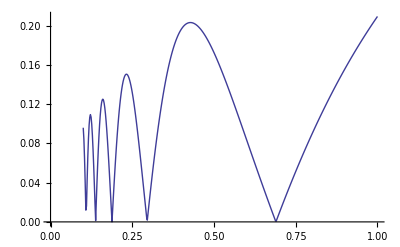

```mathematica
T1=tab1
Export["D:VB.Dat",T1]
ListPlot[T1,PlotJoined->True]
```